```mathematica
SetDirectory[NotebookDirectory[]];
```

# A⇌_k_2^k_1B reaction network

## Evaluate path integral to get pathway probability

## 1. A general function for ρ_TRP((τ⃗)_N|t=0;PATH_N) for production of species A and B. Gonna to use Mathematica double blank and pure function.

```mathematica
(*Symbol comvert string to variable*)
(*With is kind of global, it will evaluate the expression at the end*)
(*Use ; at the end of each block*)
```

### Final version, odd number N represents probability of pathway ending with species B; even number N represents probability of pathway ending with species A.

```mathematica
functionNv2[N_]:=
Module[{Neven, Nodd,output},(*Variables declaration-> local viriables*)
Nodd= Quotient[N,2]+Mod[N,2];
Neven=Quotient[N,2];
tlist=Table[StringJoin["t",IntegerString[i]], {i,1,Neven+Nodd}];
output=Product[
(*With[{var=Symbol[todd[[i]]]},*)
With[{},
Evaluate[Subscript[k, 1]*ⅇ^(-Subscript[k, 1]*Symbol[tlist[[2*i-1]]])]](*With*)
,{i,1,Nodd}](*Product*);
For[j=1,j≤Neven, j++,
output*=
With[{},
Evaluate[Subscript[k, 2]*ⅇ^(-Subscript[k, 2]*Symbol[tlist[[2*j]]])]](*With*)
](*For*);
output*=If[Mod[N,2]==1,ⅇ^(-Subscript[k, 2]*(Subscript[t, f]-∑_(i=1)^N Symbol[tlist[[i]]])),ⅇ^(-Subscript[k, 1]*(Subscript[t, f]-∑_(i=1)^N Symbol[tlist[[i]]]))]//Simplify;

(*Integral*)
For[i=N,i>1,i--,
output=Integrate[output,{Symbol[tlist⟦i⟧], Symbol[tlist⟦i-1⟧],Subscript[t, f]}]
];
If[N==0, output=ⅇ^(-Subscript[k, 1]*Subscript[t, f]),output=Integrate[output,{t1, 0,Subscript[t, f]}]];
Return[output];
](*FunctionNv2*);

(*Example*)
functionNv2[3]
```

(ⅇ^(-k_1 t_f) k_1^2 k_2 (Sinh[(k_1-k_2) t_f]+(-k_1+k_2) t_f))/(k_1-k_2)^3

```mathematica
functionNv2[0]
```

ⅇ^(-k_1 t_f)

### Fist N terms of pathway ending with species B.

```mathematica
probB=Table[functionNv2[2*i+1],{i,0,5-1}];
probB
```

{-((ⅇ^(-k_1 t_f)-ⅇ^(-k_2 t_f)) k_1)/(k_1-k_2),(ⅇ^(-k_1 t_f) k_1^2 k_2 (Sinh[(k_1-k_2) t_f]+(-k_1+k_2) t_f))/(k_1-k_2)^3,1/(6 (k_1-k_2)^5)ⅇ^(1/2 (-3 k_1+k_2) t_f) k_1^3 k_2^2 (9 Sinh[1/2 (k_1-k_2) t_f]+Sinh[3/2 (k_1-k_2) t_f]+6 Cosh[1/2 (k_1-k_2) t_f] (-k_1+k_2) t_f),-1/(72 (k_1-k_2)^7)ⅇ^((-2 k_1+k_2) t_f) k_1^4 k_2^3 (-28 Sinh[(k_1-k_2) t_f]-Sinh[2 (k_1-k_2) t_f]+6 (3+2 Cosh[(k_1-k_2) t_f]) (k_1-k_2) t_f),-1/(8640 (k_1-k_2)^9)ⅇ^(-(5 k_1+k_2) t_f) k_1^5 k_2^4 (-3 ⅇ^(5 k_1 t_f)+3 ⅇ^(5 k_2 t_f)-175 ⅇ^((4 k_1+k_2) t_f)-300 ⅇ^((3 k_1+2 k_2) t_f)+300 ⅇ^((2 k_1+3 k_2) t_f)+175 ⅇ^((k_1+4 k_2) t_f)+60 (ⅇ^((4 k_1+k_2) t_f)+6 ⅇ^((3 k_1+2 k_2) t_f)+6 ⅇ^((2 k_1+3 k_2) t_f)+ⅇ^((k_1+4 k_2) t_f)) k_1 t_f-60 (ⅇ^((4 k_1+k_2) t_f)+6 ⅇ^((3 k_1+2 k_2) t_f)+6 ⅇ^((2 k_1+3 k_2) t_f)+ⅇ^((k_1+4 k_2) t_f)) k_2 t_f)}

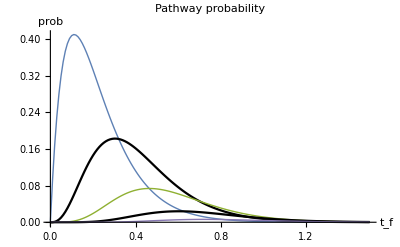

```mathematica
tfinal=1.5;
PointsB=Table[Table[{x, probB[[i]]/.{Subscript[k, 1]->10.0,Subscript[k, 2]->8.0,Subscript[t, f]->x}//Evaluate},{x,0,tfinal, 0.01}],{i,1,Length[probB]}];ListLinePlot[PointsB,PlotLabel->HoldForm[Pathway probability],AxesLabel->{HoldForm[Subscript[t, f]],prob},PlotStyle->{Thick,Black},PlotRange->All]
```

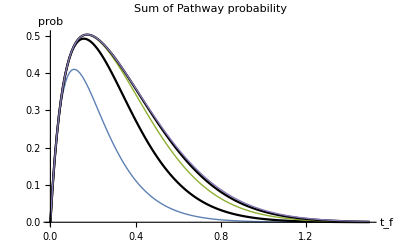

```mathematica
tfinal=1.5;
PointsBC=Table[Table[{x, Sum[probB[[j]],{j,1,i}]/.{Subscript[k, 1]->10.0,Subscript[k, 2]->8.0,Subscript[t, f]->x}//Evaluate},{x,0,tfinal, 0.01}],{i,1,Length[probB]}];ListLinePlot[PointsBC,PlotLabel->HoldForm[Sum of Pathway probability],AxesLabel->{HoldForm[Subscript[t, f]],prob},PlotStyle->{Thick,Black},PlotRange->All]
```

#### Taylor expansion.

```mathematica
probBTaylor=Table[Series[probB[[i]],{Subscript[t, f],0,9}],{i,1,Length[probB]}];
probBTaylor
```

{k_1 t_f-1/2 (k_1 (k_1+k_2)) t_f^2+1/6 k_1 (k_1^2+k_1 k_2+k_2^2) t_f^3+(k_1 (-k_1^4+k_2^4) t_f^4)/(24 (k_1-k_2))+(k_1 (k_1^5-k_2^5) t_f^5)/(120 (k_1-k_2))+(k_1 (-k_1^6+k_2^6) t_f^6)/(720 (k_1-k_2))+(k_1 (k_1^7-k_2^7) t_f^7)/(5040 (k_1-k_2))+(k_1 (-k_1^8+k_2^8) t_f^8)/(40320 (k_1-k_2))+(k_1 (k_1^9-k_2^9) t_f^9)/(362880 (k_1-k_2))+O[t_f]^10,1/6 k_1^2 k_2 t_f^3-1/6 (k_1^3 k_2) t_f^4+1/120 k_1^2 k_2 (11 k_1^2-2 k_1 k_2+k_2^2) t_f^5-1/360 (k_1^3 k_2 (13 k_1^2-6 k_1 k_2+3 k_2^2)) t_f^6+(k_1^2 k_2 (57 k_1^4-46 k_1^3 k_2+27 k_1^2 k_2^2-4 k_1 k_2^3+k_2^4) t_f^7)/5040-((k_1^3 k_2 (15 k_1^4-18 k_1^3 k_2+13 k_1^2 k_2^2-4 k_1 k_2^3+k_2^4)) t_f^8)/5040+1/362880 k_1^2 k_2 (247 k_1^6-402 k_1^5 k_2+357 k_1^4 k_2^2-164 k_1^3 k_2^3+51 k_1^2 k_2^4-6 k_1 k_2^5+k_2^6) t_f^9+O[t_f]^10,1/120 k_1^3 k_2^2 t_f^5+1/240 k_1^3 k_2^2 (-3 k_1+k_2) t_f^6+(k_1^3 k_2^2 (50 k_1^2-37 k_1 k_2+8 k_2^2) t_f^7)/5040-((k_1^3 k_2^2 (111 k_1^3-133 k_1^2 k_2+59 k_1 k_2^2-9 k_2^3)) t_f^8)/20160+(k_1^3 k_2^2 (289 k_1^4-490 k_1^3 k_2+336 k_1^2 k_2^2-106 k_1 k_2^3+13 k_2^4) t_f^9)/120960+O[t_f]^10,(k_1^4 k_2^3 t_f^7)/5040+(k_1^4 k_2^3 (-2 k_1+k_2) t_f^8)/5040+(k_1^4 k_2^3 (25 k_1^2-26 k_1 k_2+7 k_2^2) t_f^9)/60480+O[t_f]^10,(k_1^5 k_2^4 t_f^9)/362880+O[t_f]^10}

Compare pathway result with ODEs solution

```mathematica
A=Subscript[k, 2]/(Subscript[k, 1]+Subscript[k, 2])+Subscript[k, 1]/(Subscript[k, 1]+Subscript[k, 2])ⅇ^(-(Subscript[k, 1]+Subscript[k, 2])Subscript[t, f]);
B=Subscript[k, 1]/(Subscript[k, 1]+Subscript[k, 2])(1-ⅇ^(-(Subscript[k, 1]+Subscript[k, 2])Subscript[t, f]));
TaylorA=Series[A,{Subscript[t, f],0,9}]//Simplify
TaylorB=Series[B,{Subscript[t, f],0,9}]//Simplify
(*LaurentA=Series[A/.Subscript[t, f]->1/t,{t,0,10}]*)
```

1-k_1 t_f+1/2 k_1 (k_1+k_2) t_f^2-1/6 (k_1 (k_1+k_2)^2) t_f^3+1/24 k_1 (k_1+k_2)^3 t_f^4-1/120 (k_1 (k_1+k_2)^4) t_f^5+1/720 k_1 (k_1+k_2)^5 t_f^6-((k_1 (k_1+k_2)^6) t_f^7)/5040+(k_1 (k_1+k_2)^7 t_f^8)/40320-((k_1 (k_1+k_2)^8) t_f^9)/362880+O[t_f]^10

k_1 t_f-1/2 (k_1 (k_1+k_2)) t_f^2+1/6 k_1 (k_1+k_2)^2 t_f^3-1/24 (k_1 (k_1+k_2)^3) t_f^4+1/120 k_1 (k_1+k_2)^4 t_f^5-1/720 (k_1 (k_1+k_2)^5) t_f^6+(k_1 (k_1+k_2)^6 t_f^7)/5040-((k_1 (k_1+k_2)^7) t_f^8)/40320+(k_1 (k_1+k_2)^8 t_f^9)/362880+O[t_f]^10

0.5

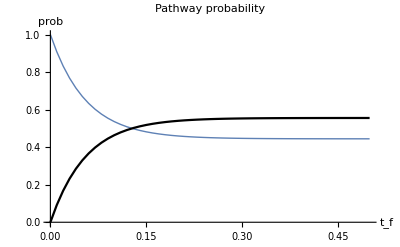

```mathematica
Subscript[k, 1]=10.0;Subscript[k, 2]=8.0; tfinal=0.5
PointsAInit=Table[{x, A/.Subscript[t, f]->x//Evaluate},{x,0,tfinal, 0.01}];
PointsBInit=Table[{x, B/.Subscript[t, f]->x//Evaluate},{x,0,tfinal, 0.01}];ListLinePlot[{PointsAInit,PointsBInit},PlotLabel->HoldForm[Pathway probability],AxesLabel->{HoldForm[Subscript[t, f]],prob},PlotStyle->{Thick,Black},PlotRange->All]
```